```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210507_time_windows_and_OR_model"];
```

```mathematica
subsetpositions=Import["subsetpositionsforsequences.mx"];
```

```mathematica
stoichioforhomosapiens=Drop[Import["../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

```mathematica
AdjmatM=stoichiometricmatrix.Transpose[stoichiometricmatrix];
NormAdjmatM=AdjmatM/.x_/;x≠0->1;
NormAdjmatM=UpperTriangularize[NormAdjmatM,1]+LowerTriangularize[NormAdjmatM,-1];
AdjmatR=Transpose[stoichioforhomosapiens].stoichioforhomosapiens;
NormAdjmatR=AdjmatR/.x_/;x≠0->1;
NormAdjmatR=UpperTriangularize[NormAdjmatR,1]+LowerTriangularize[NormAdjmatR,-1];
```

```mathematica
g01=AdjacencyGraph[NormAdjmatM,GraphLayout->"GravityEmbedding",VertexStyle->Green,ImageSize->Large];
g02=AdjacencyGraph[NormAdjmatM,GraphLayout->"CircularEmbedding"];
EdgeCount@g01
VertexCount@g01
```

3986

738

```mathematica
{g01,g02};
```

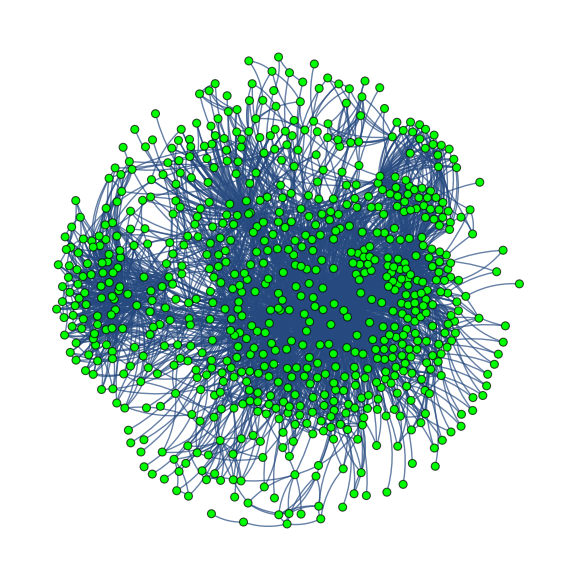

```mathematica
g01
```

```mathematica
g11=AdjacencyGraph[NormAdjmatR,GraphLayout->"GravityEmbedding",VertexStyle->Red,VertexSize->0.1,ImageSize->Large];
g12=AdjacencyGraph[NormAdjmatR,GraphLayout->"CircularEmbedding"];
EdgeCount@g11
VertexCount@g11
```

99870

1008

```mathematica
g11
```

-Graphics-

```mathematica
Table[Length@subsetpositions[[i]],{i,200}];
Table[Position[Table[Length@subsetpositions[[i]],{i,200}],a],{a,{215,158,226}}]
```

{{{7}},{{9}},{{28}}}

```mathematica
HighlightGraph[g1,{Style[subsetpositions[[7]],Red],Style[subsetpositions[[9]],Green],Style[subsetpositions[[28]],Orange]}]
```

-Graphics-